```mathematica
SetOptions[$FrontEndSession,"ExportTypesetOptions"->{"PageWidth"->5000}]
```

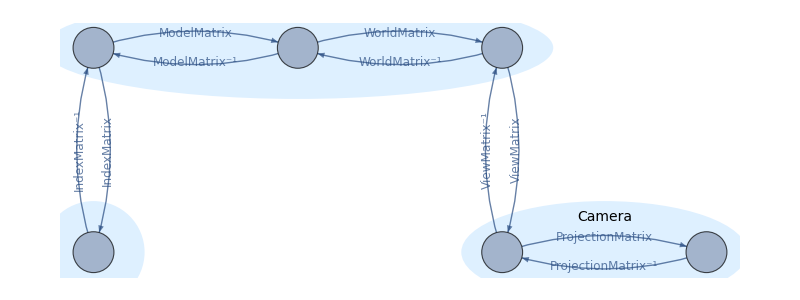

```mathematica
spaces = {{"Space", "Position", "Description", "Range"}, {"Data", {0,0}, "raw data numbers", "generally (-inf, inf), ([0,1] for textures)"}, {"Model", {1,0}, "model space coordinates", "(data min, data max)"}, {"World", {2,0}, "world space coordinates", "(-inf, inf)"}, {"View", {2,-1}, "view space coordinates", "(-inf, inf)"}, {"Clip", {3,-1}, "clip space coordinates", "[-1,1]"}, {"Index", {0,-1}, "voxel index coordinates", "[0, number of voxels)"}};
transforms={{"From Space", "To Space", "Transform", "Entity", "Member"}, {"Data", "Model", "ModelMatrix", "const SpatialEntity<N>*", "entity_"}, {"Model", "World", "WorldMatrix", "const SpatialEntity<N>*", "entity_"}, {"World", "View", "ViewMatrix", "const CameraND<N>*", "camera_"}, {"View", "Clip", "ProjectionMatrix", "const CameraND<N>*", "camera_"}, {"Data", "Index", "IndexMatrix", "const StructuredGridEntity<N>*", "entity_"}}; 

spacedict = <|Table[spaces[[i,1]]->AssociationThread[spaces[[1]],spaces[[i]]],{i,2,Length[spaces]}]|>;
graph = Graph[transforms[[2;;]]/.{from_?StringQ,to_?StringQ,transform_,x_,y_}:>Sequence[from->to,to->from]];
posList = spaces[[2;;,{1,2}]]/.{space_,pos_}:>space->pos;
vertexPos=VertexList[graph]/.posList;
edgeLables = transforms[[2;;]]/.{from_?StringQ,to_?StringQ,transform_,x_,y_}:>Sequence[
from ->to->Rotate[transform,VectorAngle[{1,0},(to/.posList)-(from/.posList)]],
to->from->Rotate[Superscript[transform,"-1"],VectorAngle[{1,0},(to/.posList)-(from/.posList)]]];
gview=Graph[graph,
VertexCoordinates->vertexPos,
VertexLabels->Placed["Name",{0.5,0.5}],
VertexSize->Medium,
VertexLabelStyle->Directive[12],
EdgeLabels->edgeLables,
EdgeLabelStyle->Directive[12,Background->White],
ImageSize->800,
Prolog->{
LightBlue,Ellipsoid[spacedict["Model","Position"],{1.25,0.25}],
Black,Text[Style["Spatial",14],spacedict["Model","Position"]+{0,0.17}],
LightBlue,Ellipsoid[spacedict["Index","Position"],{.25,0.25}],
Black,Text[Style["Structured",14],spacedict["Index","Position"]+{0,-0.17}],
LightBlue,Ellipsoid[0.5*(spacedict["View","Position"]+spacedict["Clip","Position"]),{.7,0.25}],
Black,Text[Style["Camera",14],0.5*(spacedict["View","Position"]+spacedict["Clip","Position"])+{0,0.17}]}
]
```

```mathematica
g1=Grid[spaces[[All,{1,3,4}]], Dividers->{False, {False,1}}, Alignment->Left]
g2=Grid[transforms, Dividers->{False, {False,1}}, Alignment->Left]
```

Space | Description | Range
Data | raw data numbers | generally (-inf, inf), ([0,1] for textures)
Model | model space coordinates | (data min, data max)
World | world space coordinates | (-inf, inf)
View | view space coordinates | (-inf, inf)
Clip | clip space coordinates | [-1,1]
Index | voxel index coordinates | [0, number of voxels)

From Space | To Space | Transform | Entity | Member
Data | Model | ModelMatrix | const SpatialEntity<N>* | entity_
Model | World | WorldMatrix | const SpatialEntity<N>* | entity_
World | View | ViewMatrix | const CameraND<N>* | camera_
View | Clip | ProjectionMatrix | const CameraND<N>* | camera_
Data | Index | IndexMatrix | const StructuredGridEntity<N>* | entity_

```mathematica
ExportString[OutputForm[g1],"Text"]
ExportString[OutputForm[g2],"Text"]
```

Space   Description               Range

Data    raw data numbers          generally (-inf, inf), ([0,1] for textures)

Model   model space coordinates   (data min, data max)

World   world space coordinates   (-inf, inf)

View    view space coordinates    (-inf, inf)

Clip    clip space coordinates    [-1,1]

Index   voxel index coordinates   [0, number of voxels)

From Space   To Space   Transform          Entity                           Member

Data         Model      ModelMatrix        const SpatialEntity<N>*          entity_

Model        World      WorldMatrix        const SpatialEntity<N>*          entity_

World        View       ViewMatrix         const CameraND<N>*               camera_

View         Clip       ProjectionMatrix   const CameraND<N>*               camera_

Data         Index      IndexMatrix        const StructuredGridEntity<N>*   entity_

```mathematica
FindTransform[from_, to_]:=Module[{path,trans},
path=FindShortestPath[graph,from,to];
trans=EdgeList[PathGraph[path,DirectedEdges->True]]/. 
(transforms[[2;;]]/.{f_?StringQ,t_?StringQ,transform_,x_,y_}:>Sequence[f ->t->transform,t->f->Inv[transform]]);
(* Apply the matrices in the oposite order *)
trans = Reverse[trans];
(* Avoid calculating inverses A^-1*B^-1 = (B*B)^-1 *) 
trans = trans//.{x___,Inv[A_],Inv[B_],y___}:>{x,Inv[{B,A}],y};
(* Add function calls *)
trans = trans/.x_?StringQ:>"get"<>x<>"()";
(* Apply multipilcation *) 
trans = trans//.{{A_?StringQ}:>A, {x___,A_?StringQ,B_?StringQ,y___}:>{x,A<>"*"<>B,y}};
(* Call inv *)
trans = trans/.{Inv[x_]:>"glm::inverse("<>x<>")"};
(* Apply multipilcation *) 
trans = trans//.{{A_?StringQ}:>A, {x___,A_?StringQ,B_?StringQ,y___}:>{x,A<>"*"<>B,y}};
trans 
]
```

```mathematica
TableForm[{#[[1]],#[[2]],FindTransform@@#}&/@Permutations[spaces[[2;;,1]],{2}],TableHeadings->{None,{"From","To","Operation"}}]
```

From | To | Operation
Data | Model | getModelMatrix()
Data | World | getWorldMatrix()*getModelMatrix()
Data | View | getViewMatrix()*getWorldMatrix()*getModelMatrix()
Data | Clip | getProjectionMatrix()*getViewMatrix()*getWorldMatrix()*getModelMatrix()
Data | Index | getIndexMatrix()
Model | Data | glm::inverse(getModelMatrix())
Model | World | getWorldMatrix()
Model | View | getViewMatrix()*getWorldMatrix()
Model | Clip | getProjectionMatrix()*getViewMatrix()*getWorldMatrix()
Model | Index | getIndexMatrix()*glm::inverse(getModelMatrix())
World | Data | glm::inverse(getWorldMatrix()*getModelMatrix())
World | Model | glm::inverse(getWorldMatrix())
World | View | getViewMatrix()
World | Clip | getProjectionMatrix()*getViewMatrix()
World | Index | getIndexMatrix()*glm::inverse(getWorldMatrix()*getModelMatrix())
View | Data | glm::inverse(getViewMatrix()*getWorldMatrix()*getModelMatrix())
View | Model | glm::inverse(getViewMatrix()*getWorldMatrix())
View | World | glm::inverse(getViewMatrix())
View | Clip | getProjectionMatrix()
View | Index | getIndexMatrix()*glm::inverse(getViewMatrix()*getWorldMatrix()*getModelMatrix())
Clip | Data | glm::inverse(getProjectionMatrix()*getViewMatrix()*getWorldMatrix()*getModelMatrix())
Clip | Model | glm::inverse(getProjectionMatrix()*getViewMatrix()*getWorldMatrix())
Clip | World | glm::inverse(getProjectionMatrix()*getViewMatrix())
Clip | View | glm::inverse(getProjectionMatrix())
Clip | Index | getIndexMatrix()*glm::inverse(getProjectionMatrix()*getViewMatrix()*getWorldMatrix()*getModelMatrix())
Index | Data | glm::inverse(getIndexMatrix())
Index | Model | getModelMatrix()*glm::inverse(getIndexMatrix())
Index | World | getWorldMatrix()*getModelMatrix()*glm::inverse(getIndexMatrix())
Index | View | getViewMatrix()*getWorldMatrix()*getModelMatrix()*glm::inverse(getIndexMatrix())
Index | Clip | getProjectionMatrix()*getViewMatrix()*getWorldMatrix()*getModelMatrix()*glm::inverse(getIndexMatrix())

```mathematica
ivwclass=StringTemplate[
"/*********************************************************************************
 *
 * Inviwo - Interactive Visualization Workshop
 *
 * Copyright (c) 2012-2022 Inviwo Foundation
 * All rights reserved.
 *
 * Redistribution and use in source and binary forms, with or without
 * modification, are permitted provided that the following conditions are met:
 *
 * 1. Redistributions of source code must retain the above copyright notice, this
 * list of conditions and the following disclaimer.
 * 2. Redistributions in binary form must reproduce the above copyright notice,
 * this list of conditions and the following disclaimer in the documentation
 * and/or other materials provided with the distribution.
 *
 * THIS SOFTWARE IS PROVIDED BY THE COPYRIGHT HOLDERS AND CONTRIBUTORS \"AS IS\" AND
 * ANY EXPRESS OR IMPLIED WARRANTIES, INCLUDING, BUT NOT LIMITED TO, THE IMPLIED
 * WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE ARE
 * DISCLAIMED. IN NO EVENT SHALL THE COPYRIGHT OWNER OR CONTRIBUTORS BE LIABLE FOR
 * ANY DIRECT, INDIRECT, INCIDENTAL, SPECIAL, EXEMPLARY, OR CONSEQUENTIAL DAMAGES
 * (INCLUDING, BUT NOT LIMITED TO, PROCUREMENT OF SUBSTITUTE GOODS OR SERVICES;
 * LOSS OF USE, DATA, OR PROFITS; OR BUSINESS INTERRUPTION) HOWEVER CAUSED AND
 * ON ANY THEORY OF LIABILITY, WHETHER IN CONTRACT, STRICT LIABILITY, OR TORT
 * (INCLUDING NEGLIGENCE OR OTHERWISE) ARISING IN ANY WAY OUT OF THE USE OF THIS
 * SOFTWARE, EVEN IF ADVISED OF THE POSSIBILITY OF SUCH DAMAGE.
 *
 *********************************************************************************/

#pragma once

#include <inviwo/core/common/inviwocoredefine.h>
#include <inviwo/core/datastructures/camera.h>
#include <inviwo/core/util/exception.h>
#include <inviwo/core/util/fmtutils.h>

#include <glm/matrix.hpp>

#include <iosfwd>

namespace inviwo {
// clang-format off
/**
 * This file is auto generated using tools/codegen/coordinatetransforms.nb
 *
 * Space   Description               Range
 * ===================================================================================
 * Data    raw data numbers          generally (-inf, inf), ([0,1] for textures)
 * Model   model space coordinates   (data min, data max)
 * World   world space coordinates   (-inf, inf)
 * View    view space coordinates    (-inf, inf)
 * Clip    clip space coordinates    [-1,1]
 * Index   voxel index coordinates   [0, number of voxels)
 *
 * From Space   To Space   Transform          Entity                           Member
 * ===================================================================================
 * Data         Model      ModelMatrix        const SpatialEntity<N>*          entity_
 * Model        World      WorldMatrix        const SpatialEntity<N>*          entity_
 * World        View       ViewMatrix         const CameraND<N>*               camera_
 * View         Clip       ProjectionMatrix   const CameraND<N>*               camera_
 * Data         Index      IndexMatrix        const StructuredGridEntity<N>*   entity_
 * 
 * 
 *  ┌───────────────────────────────────────────────────────────┐
 *  │                          Spatial                          │
 *  │               ModelM.               WorldM.               │                         
 *  │   ┌────────┐──────────▶┌────────┐───────────▶┌────────┐   │                         
 *  │   │        │           │        │            │        │   │                         
 *  │   │  Data  │           │ Model  │            │ World  │   │                         
 *  │   │        │ ModelM.-1 │        │  WorldM.-1 │        │   │                         
 *  │   └────────┘◀──────────└────────┘◀───────────└────────┘   │                         
 *  │   │        ▲                                 │        ▲   │                         
 *  └───┼────────┼─────────────────────────────────┼─────   ┼───┘                         
 *      │      I │                                 │      V │                             
 *    I │      n │                               V │      i │                             
 *    n │      d │                               i │      e │                             
 *    d │      e │                               e │      w │                             
 *    e │      x │                               w │      M │                             
 *    x │      M │                               M │      - │                             
 *    M │      - │                                 │      1 │                             
 *      │      1 │                                 │        │                             
 *  ┌───┼────────┼────┐                        ┌───┼────────┼────────────────────────────┐
 *  │   │        │    │                        │   │        │                            │
 *  │   ▼        │    │                        │   ▼        │  ProjectionM               │
 *  │   ┌────────┐    │                        │   ┌────────┐──────────────▶┌────────┐   │
 *  │   │        │    │                        │   │        │               │        │   │
 *  │   │ Index  │    │                        │   │  View  │               │  Clip  │   │
 *  │   │        │    │                        │   │        │ ProjectionM-1 │        │   │
 *  │   └────────┘    │                        │   └────────┘◀──────────────└────────┘   │
 *  │                 │                        │                                         │
 *  │   Structured    │                        │                 Camera                  │
 *  └─────────────────┘                        └─────────────────────────────────────────┘
 */

template <unsigned int N>
class SpatialEntity;

template <unsigned int N>
class StructuredGridEntity;

namespace util {

class Camera2D {
public:
    Camera2D() : view_(1.0f), projection_(1.0f) {}
    const glm::mat3& getViewMatrix() const { return view_; }
    const glm::mat3& getProjectionMatrix() const { return projection_; }

private:
    glm::mat3 view_;
    glm::mat3 projection_;
};

template <unsigned int N>
struct cameratype {};

template <>
struct cameratype<2> {
    typedef Camera2D type;
};

template <>
struct cameratype<3> {
    typedef Camera type;
};
}
template <unsigned int N>
using CameraND = typename util::cameratype<N>::type;

enum class CoordinateSpace {
    Data, Model, World, Index, Clip, View
};

IVW_CORE_API std::string_view enumToStr(CoordinateSpace s);

IVW_CORE_API std::ostream& operator<<(std::ostream& ss, CoordinateSpace s);

`content`
// clang-format on
}  // namespace inviwo

template <>
struct fmt::formatter<inviwo::CoordinateSpace> : inviwo::FlagFormatter<inviwo::CoordinateSpace> {};
"
];
```

```mathematica
ClearAll[ApplyTemplate];
ApplyTemplate[t_,sel_,dict_:<||>,alias_:{}]:=Module[{keys,assoc,pairs},
keys = t/.TemplateObject[x_,___]:>Cases[x,TemplateSlot[s_]:>s];
pairs=Permutations[sel,{2}];
TemplateApply@TemplateSequence[t,
assoc=Table[
Join[
pair/.{from_,to_}:><| Map[#->spacedict@@StringSplit[#,x:("from"|"to"):>(x/.{"from"->from,"to"->to})]&,keys]|>,
pair/.{from_,to_}:><|"implementation"->FindTransform[from,to]|>,
KeyDrop[dict,{"alias","selection"}]],
{pair,pairs}];
Union[assoc,Map[#/.alias&,assoc,{2}]],
Delimiters->"\n"]
];

transformTemplate = StringTemplate[
"    /**
     * Returns the matrix transformation mapping from `fromDescription`
     * to `toDescription`, i.e. from `fromRange` to `toRange`
     */
    virtual glm::mat<N+1, N+1, float> get`fromSpace`To`toSpace`Matrix() const = 0;"
];

transformTemplateSlim = StringTemplate[
"    virtual glm::mat<N+1, N+1, float> get`fromSpace`To`toSpace`Matrix() const = 0;"
];

classTemplate = TemplateObject[{
"template<unsigned int N>\n",
"class ",TemplateSlot["name"],TemplateIf[TemplateSlot["base"]!="—",{" : public ",TemplateSlot["base"],"<N>"}]," {\n",
"public:\n",
"    virtual ~",TemplateSlot["name"],"() = default;\n",
"    virtual ",TemplateSlot["name"],"<N>* clone() const = 0;\n",
"    /**\n",
"     * Returns the matrix transformation mapping from \"from\" coordinates\n",
"     * to \"to\" coordinates\n",
"     */\n",
"    virtual glm::mat<N + 1, N + 1, float> getMatrix(CoordinateSpace from, CoordinateSpace to) const;\n",
TemplateSlot["content"],"\n",
"};"
},InsertionFunction->TextString,CombinerFunction->StringJoin];

transformTemplateDecl = StringTemplate[
"    virtual glm::mat<N+1, N+1, float> get`fromSpace`To`toSpace`Matrix() const;"
];

getterTemplateDecl = StringTemplate[
"    virtual glm::mat<N+1, N+1, float> get`transform`() const;"
];

getterTemplateImpl = TemplateObject[{
"template <unsigned int N>\nglm::mat<N+1, N+1, float> ",
TemplateSlot["name"],"<N>::get",TemplateSlot["transform"],"() const {\n",
"    return ",TemplateSlot["member"],TemplateSlot["op"],"get",TemplateSlot["transform"],"();\n",
"}"},
InsertionFunction->TextString,CombinerFunction->StringJoin];

transformTemplateImpl = StringTemplate[
StringJoin[{
"template <unsigned int N>\n",
"glm::mat<N+1, N+1, float> `name`Impl<N>::get`fromSpace`To`toSpace`Matrix() const {\n",
"    return `implementation`;\n",
"}\n"}
]
];

memberSetTemplateDecl =StringTemplate[ "    void set`Member`(`type`& `member`);"];
memberSetTemplateImpl =StringTemplate[ 
"template <unsigned int N>
void `name`Impl<N>::set`Member`(`type`& `member`) {
    `member`_ = &`member`;
}"];

classTemplateImplDecl = TemplateObject[{
"template<unsigned int N>\n",
"class ",TemplateSlot["name"],TemplateIf[TemplateSlot["base"]!="—",{" : public ",TemplateSlot["base"],"<N>"}]," {\n",
"public:\n",
"    ",TemplateSlot["name"],"(",TemplateSlot["constructorargs"],");\n",
"    ",TemplateSlot["name"],"(const ",TemplateSlot["name"],"<N>& rhs) = default;\n",
"    ",TemplateSlot["name"],"<N>& operator=(const ",TemplateSlot["name"],"<N>& that) = default;\n",
"    virtual ",TemplateSlot["name"],"<N>* clone() const;\n",
"    virtual ~",TemplateSlot["name"],"(){}\n\n",
TemplateSlot["content"],"\n\n",
"protected:\n",
TemplateSlot["getters"],"\n\n",
"private:\n",
TemplateSlot["members"],"\n",
"};\n"}];


classTemplateImplImpl = TemplateObject[{
"/*********************************************************************************\n",
" *  Implementations\n",
" *  ",TemplateSlot["name"],"\n",
" *********************************************************************************/\n",
"\n",
"template<unsigned int N>\n",
TemplateSlot["name"],"<N>::",TemplateSlot["name"],"(",TemplateSlot["constructorargs"],")\n",
TemplateIf[TemplateSlot["base"]!="—",{"    : ",TemplateSlot["base"] ,"<N>()\n    , "},"    : "],
TemplateSlot["initmember"]," {}\n",
"\n",
"template<unsigned int N>\n",
TemplateSlot["name"],"<N>* ",TemplateSlot["name"],"<N>::clone() const {\n",
"    return new ",TemplateSlot["name"],"<N>(*this);\n",
"}\n",
"\n",
TemplateSlot["implementation"]
},InsertionFunction->TextString,CombinerFunction->StringJoin];

spatial = <|
"name"->"SpatialCoordinateTransformer",
"args"->{{"const SpatialEntity<N>","entity"}},
"selection"->{"Data","Model","World"},
"alias"->{}
|>;
structured =<|
"name"->"StructuredCoordinateTransformer",
"base"->spatial["name"],
"args"->{{"const StructuredGridEntity<N>","entity"}},
 "selection"-> {"Index","Data","Model","World"},
"alias"->{"Data"->"Texture"}
|>;
camera=<|
"name"->"SpatialCameraCoordinateTransformer",
"base"->spatial["name"], 
"args"->{{"const SpatialEntity<N>","entity"},{"const CameraND<N>","camera"}},
"selection"-> {"Data","Model","World","View","Clip"},
"alias"->{}
|>;
structuredcamera=<|
"name"->"StructuredCameraCoordinateTransformer",
"base"->camera["name"],
"args"->{{"const StructuredGridEntity<N>","entity"},{"const CameraND<N>","camera"}},
"selection"-> {"Index","Data","Model","World","View","Clip"},
"alias"->{"Data"->"Texture"}
|>;

ClearAll[LowerCaseFirstLetter];
LowerCaseFirstLetter[x_]:= ToLowerCase[StringTake[x,1]]<>StringTake[x,2;;];
UpperCaseFirstLetter[x_]:= ToUpperCase[StringTake[x,1]]<>StringTake[x,2;;];
ClearAll[getInvolvedTransforms]
getInvolvedTransforms[transforms_,sel_,dict_:<||>]:=Module[{trans,pairs,members,entities},
trans=<|transforms/.{f_?StringQ,t_?StringQ,m_,x_,y_}:>{f->t->m}|>;
entities = <|#/.{f_?StringQ,t_?StringQ,m_,e_,mem_}:>{m->e}&/@transforms|>;
members = <|#/.{f_?StringQ,t_?StringQ,m_,e_,mem_}:>{m->mem}&/@transforms|>;
pairs=Permutations[sel,{2}]/.{f_,t_}:>f->t;
trans/@pairs//.Missing[___]:>Sequence[]/.x_?StringQ:>Join[<|"transform"->x,"op"->If[StringTake[entities[x],-1]=="*","->","."],"member"->members[x],"entity"->entities[x]|>,dict]
];


spacelist = {spatial,structured,camera, structuredcamera};
impldict = <|
"name"->#["name"]<>"Impl",
"base"->#["name"],
"constructorargs"->StringJoin[Riffle[#[[1]]<>"& "<> #[[2]]&/@#["args"],", "]],
"members"->StringJoin[Riffle["    "<>#[[1]]<>"* " <>#[[2]]<>"_;" &/@#["args"],"\n"]],
"initmember"->StringJoin[Riffle[#[[2]]<>"_{&"<>#[[2]]<>"}" &/@#["args"],"\n    , "]],

"getters"->StringJoin@TemplateApply@TemplateSequence[getterTemplateDecl,
getInvolvedTransforms[transforms[[2;;]],#["selection"]],Delimiters->"\n"],
"content"->StringJoin[
StringJoin@TemplateApply@TemplateSequence[memberSetTemplateDecl,
Map[Function[{arg},<|"name"->#["name"],"type"->arg[[1]],"Member"->UpperCaseFirstLetter[arg[[2]]],"member"->arg[[2]]|>],#["args"]],Delimiters->"\n"],
"\n\n",
StringJoin@ApplyTemplate[transformTemplateDecl,#["selection"],<||>,#["alias"]]
],
"implementation"->StringJoin[
StringJoin@TemplateApply@TemplateSequence[getterTemplateImpl,
getInvolvedTransforms[transforms[[2;;]],#["selection"],<|"name"->#["name"]<>"Impl"|>],Delimiters->"\n"],

"\n\n",

StringJoin@TemplateApply@TemplateSequence[memberSetTemplateImpl,
Map[Function[{arg},<|"name"->#["name"],"type"->arg[[1]],"Member"->UpperCaseFirstLetter[arg[[2]]],"member"->arg[[2]]|>],#["args"]],Delimiters->"\n"],

"\n\n",

StringJoin@ApplyTemplate[transformTemplateImpl,#["selection"],#,#["alias"]]
]
|>&/@spacelist;

basecode = StringJoin@TemplateApply@TemplateSequence[classTemplate,
Join[#,<|"content"->StringJoin@ApplyTemplate[transformTemplate,#["selection"],<||>,#["alias"]]|>]&/@
spacelist,Delimiters->"\n\n"];

classcode=StringJoin@TemplateApply@TemplateSequence[classTemplateImplDecl,impldict,Delimiters->"\n\n"];
implcode=StringJoin@TemplateApply@TemplateSequence[classTemplateImplImpl,impldict,Delimiters->"\n\n"];

baseClassTemplateImpl = TemplateObject[{
"template<unsigned int N>\n",
"glm::mat<N + 1, N + 1, float> ",TemplateSlot["name"],"<N>::getMatrix(CoordinateSpace from, CoordinateSpace to) const {\n",
"    switch (from) {\n",
TemplateSlot["content"],"\n",
"        default:\n",
"            throw Exception(IVW_CONTEXT, \"getMatrix is not available for the given space: {}\", from);\n",
"    }\n", 
"}\n"
},InsertionFunction->TextString,CombinerFunction->StringJoin];

switchFromTemplate = TemplateObject[{
"        case CoordinateSpace::", TemplateSlot["fromSpace"],":\n",
"            switch (to) {\n",
TemplateSlot["content"],"\n",
"                default:\n",
"                    throw Exception(IVW_CONTEXT, \"getMatrix is not available for the given spaces: {} to {}\", \n",
"                                    CoordinateSpace::", TemplateSlot["fromSpace"] ,", to);\n",
"            }"
},InsertionFunction->TextString,CombinerFunction->StringJoin
];
switchToTemplate = TemplateObject[{
"                case CoordinateSpace::", TemplateSlot["toSpace"],":\n",
TemplateIf[TemplateSlot["fromSpace"]== TemplateSlot["toSpace"],
"                    return glm::mat<N + 1, N + 1, float>(1.0f);",
{"                    return get", TemplateSlot["fromSpace"],"To", TemplateSlot["toSpace"],"Matrix();"}]
},InsertionFunction->TextString,CombinerFunction->StringJoin
];

baseimpl = StringJoin@TemplateApply@TemplateSequence[baseClassTemplateImpl,
Function[{space},Join[space,<|"content"->StringJoin@TemplateApply@TemplateSequence[switchFromTemplate,Map[Function[{from},<|"fromSpace"->from, "content"-> 
StringJoin@TemplateApply@TemplateSequence[switchToTemplate, Map[<|"fromSpace"->from, "toSpace"->#|>&, space["selection"]],Delimiters->"\n"]
|>],space["selection"]],Delimiters->"\n"]|>]]/@
spacelist,Delimiters->"\n"];

baseimpl = StringJoin[{
"#include <warn/push>\n",
"#include <warn/ignore/switch-enum>\n", 
baseimpl, 
"#include <warn/pop>\n"}];

code =StringJoin[{basecode,"\n\n",baseimpl,"\n\n",  classcode,"\n\n", implcode}];
text = ivwclass[<|"content"->code|>];
Export["C:/Users/petst55.AD/Documents/Inviwo/inviwo/include/inviwo/core/datastructures/coordinatetransformer.h",text,"Text"]
```

C:/Users/petst55.AD/Documents/Inviwo/inviwo/include/inviwo/core/datastructures/coordinatetransformer.h